# Dynamics of Triaxially-deformed Freely-precessing Neutron Stars

## Section 2 Free precession of triaxial rigid bodies

### Equations of motion and qualitative analyses

The configuration of the rigid body

The kinematics of the rigid body

ω_1==ϕ̇ sinθsinψ+θ̇ cosψ
ω_2==ϕ̇ sinθcosψ-θ̇ sinψ
ω_3==ϕ̇ cosθ+ψ̇

The dynamical equations of motion

|  I_1 dω_1/dt==(I_2-I_3)ω_2 ω_3 
                                   |  I_2 dω_2/dt==(I_3-I_1)ω_3 ω_1 
   |  I_3 dω_3/dt==(I_1-I_2)ω_1 ω_2

-Graphics-

We assume I_1< I_2< I_3. The tail of the angular momentum  can only move on the intersecting lines,

2E I_1 < J^2 < 2E I_3

1. When 2E I_1 < J^2 << 2E I_2 , the tail of the angular momentum moves around e_1 along a closed curve in the body frame.

2. When  2E I_1 <<J^2 = 2E I_2 , the spinning ellipsoid is not stable, the angular momentum vector moves in a great circle. This effect can make the force free rigid body twist around, which is called tennis-racket effect, or Janibekov effect (a Soviet astronaut, who found this bizarre effect in spacecraft).
3. When J^2 - 2E I_2 > 0, the tail of the angular momentum moves around e_3 along a closed curve in the body frame.

### Section 2.1 The analytical solution in the body frame (J^2 - 2E I_2 > 0)

We have three Euler equations, we can substitute two equations with two first integrals. It shows that

ω_1^2 |  ==[(2E I_3-J^2)-I_2(I_3-I_2)ω_2^2]/(I_1(I_3-I_1)) 
ω_3^2 | ==[(J^2-2E I_1)-I_2(I_2-I_1)ω_2^2]/(I_3(I_3-I_1))

and ω_2 satisfies

We define

|                      τ==t √(((I_3-I_2)(J^2-2E I_1))/(I_1 I_2 I_3)) 
                                    |      s==ω_2 √((I_2(I_3-I_2))/(2E I_3-J^2))
   |                     k^2==m=((I_2-I_1)(2E I_3-J^2))/((I_3-I_2)(J^2-2E I_1))

Integrating the differential equation of ω_2, we could find that

τ =  ∫_0^s ds/(√((1-s^2)(1-k^2 s^2)))ⅆs

This is a Jacobian elliptic function, where s is Jacobian amplitude and k is elliptic modulus.  The inverse of the elliptic function gives us the time evolution of s.

s = sn(τ),   cn(τ) = √(1-sn^2 τ) ,  dn(τ) = √(1 - k^2 sin^2 τ)

The three functions are periodic with respect to τ, and  the period is

T = 4 K

where K is the elliptic integral of the first kind

K = ∫_0^1 ds/(√((1-s^2)(1-k^2 s^2)))ⅆs

```mathematica
EllipticK[0]
EllipticK[0.5]
EllipticK[1]
```

π/2

1.85407

ComplexInfinity

The evolutions of the angular velocities in the body frame are

### The angular velocities in the body frame (Example in Fig 2)

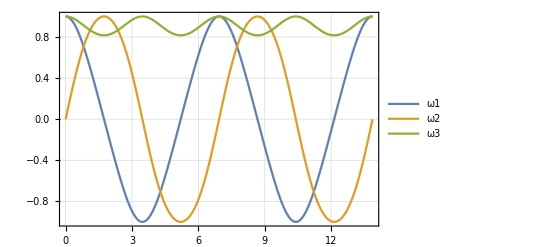

```mathematica
I1=1;
I2=2;
I3=3;
a=1;
w20=0;
b=1;
J= (I1^2*a^2+I2^2*w20^2+I3^2*b^2)^0.5;
E0=1/2 I1*a^2+1/2 I2*w20^2+1/2 I3*b^2;
m=((I2-I1)(2E0*I3-J^2))/((I3-I2)(J^2-2E0*I1));
taut=√(((I3-I2)(J^2-2E0*I1))/(I1*I2*I3));(* the scale factor in Eq.(12)*)
K=EllipticK[m];
T=4*K*((I1*I2*I3)/((I3-I2)*(J^2-2*E0*I1)))^0.5;
n=2;(* how many free precession period*)
dt=n*T/1000;
time=Table[t,{t,0,n*T,dt}];
w1=Table[a*JacobiCN[t*taut,m],{t,0,n*T,dt}];
w2=Table[a*√((I1(I3-I1))/(I2(I3-I2)))*JacobiSN[t*taut,m],{t,0,n*T,dt}];
w3=Table[b*JacobiDN[t*taut,m],{t,0,n*T,dt}];
ω1=Transpose@{time,w1};
ω2=Transpose@{time,w2};
ω3=Transpose@{time,w3};
ListPlot[{ω1,ω2,ω3},Joined->True,PlotLegends->{"ω1","ω2","ω3"},PlotTheme->"Detailed"]
```

The free precession period

```mathematica
T
```

6.93567

### The analytical solution in the inertia frame

### The analytical solution of the Euler angles (example in Fig 2)

Power::infy: 碰到无穷表达式 1/0..

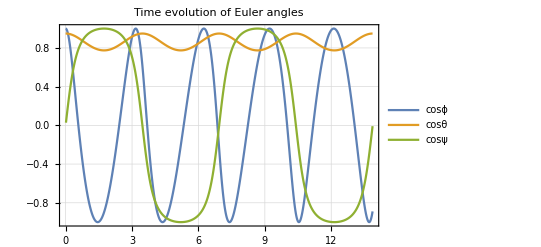

```mathematica
I1=1;
I2=2;
I3=3;
a=1;
w20=0;
b=1;
J= (I1^2*a^2+I2^2*w20^2+I3^2*b^2)^0.5;
E0=1/2 I1*a^2+1/2 I2*w20^2+1/2 I3*b^2;
m=((I2-I1)(2E0*I3-J^2))/((I3-I2)(J^2-2E0*I1));
taut=√(((I3-I2)(J^2-2E0*I1))/(I1*I2*I3));
K=EllipticK[m];
T=4*K*((I1*I2*I3)/((I3-I2)*(J^2-2*E0*I1)))^0.5;
x1=I* (I3*b)/(I1*a);
α= Re[InverseJacobiSN[x1,m]/I/K/2];
q= Exp[-π* EllipticK[1-m]/EllipticK[m]];
T1=2π/Re[(J/I1+2*I*π/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])];
n=2;
dt=n*T/1001.3;
time=Table[t,{t,0,n*T,dt}];
cosθ=Table[I3*b/J*JacobiDN[t*taut,m],{t,0,n*T,dt}];
sinθ=Sin[ArcCos[Table[I3*b/J*JacobiDN[t*taut,m],{t,0,n*T,dt}]]];
cosψ=Cos[ArcTan[Table[√((I1(I3-I2))/(I2(I3-I1)))JacobiCN[t*taut,m]/JacobiSN[t*taut,m],{t,0,n*T,dt}]]]*Sign[Floor[time/T]*T+T/2-time];
sinψ=Sin[ArcTan[Table[√((I1(I3-I2))/(I2(I3-I1)))JacobiCN[t*taut,m]/JacobiSN[t*taut,m],{t,0,n*T,dt}]]]*Sign[Floor[time/T]*T+T/2-time];
cosϕ1=Cos[ArcCos[Table[Re[EllipticTheta[4,2*π/T*t+π*α*I,q]/EllipticTheta[4,2*π/T*t-π*α*I,q]],{t,0,n*T,dt}]]/2];
sinϕ1=Sin[ArcSin[Table[Im[EllipticTheta[4,2*π/T*t+π*α*I,q]/EllipticTheta[4,2*π/T*t-π*α*I,q]],{t,0,n*T,dt}]]/2];
sinϕ2=Sin[Table[(2π)/T1*t,{t,0,n*T,dt}]];
cosϕ2=Cos[Table[(2π)/T1*t,{t,0,n*T,dt}]];
cosϕ=cosϕ1*cosϕ2-sinϕ1*sinϕ2;
first=Transpose@{time,cosϕ};
second=Transpose@{time,cosθ};
third=Transpose@{time,cosψ};
ListPlot[{first,second,third},Joined->True, PlotLegends->{"cosϕ","cosθ","cosψ"},PlotLabel->"Time evolution of Euler angles",PlotTheme->"Detailed"]
```

### Appendix A: Check the typos in the book of Landau and Lifshitz

Our series definition of the theta function

The series definition of the theta function in Mathematica

We check the results in Landau & Lifshitz 1960 by applying the time derivative of Euler angle ϕ

```mathematica
d1=Re[Table[(π EllipticThetaPrime[4,(2 π t)/T-I π α,q])/(T EllipticTheta[4,(2 π t)/T-I π α,q]I)-(π EllipticThetaPrime[4,(2 π t)/T+I π α,q])/(T EllipticTheta[4,(2 π t)/T+I π α,q]I),{t,0,T,0.001}]];
d2=Re[J/I1-(2 π I)/T EllipticThetaPrime[4,I π α,q]/EllipticTheta[4,I π α,q]];
time1=Table[t,{t,0,T,0.001}];
dϕ1=Transpose@{time1,d1+d2};
```

The time derivative of ϕ can also be expressed explicitly as

```mathematica
I1=1;
I2=2;
I3=3;
a=1;
w20=0;
b=1;
J= (I1^2*a^2+I2^2*w20^2+I3^2*b^2)^0.5;
E0=1/2 I1*a^2+1/2 I2*w20^2+1/2 I3*b^2;
k2=((I2-I1)(2E0*I3-J^2))/((I3-I2)(J^2-2E0*I1));
taut=√(((I3-I2)(J^2-2E0*I1))/(I1*I2*I3));
K=EllipticK[k2];
T=4*K*((I1*I2*I3)/((I3-I2)*(J^2-2*E0*I1)))^0.5;
n=1;
dt=0.001;
x1=I* (I3*b)/(I1*a);
α= Re[InverseJacobiSN[x1,k2]/I/K/2];
q= Exp[-π* EllipticK[1-k2]/EllipticK[k2]];
w1=Table[a*JacobiCN[t*taut,k2],{t,0,n*T,dt}];
w2=Table[a*√((I1(I3-I1))/(I2(I3-I2)))*JacobiSN[t*taut,k2],{t,0,n*T,dt}];
w3=Table[b*JacobiDN[t*taut,k2],{t,0,n*T,dt}];
time2=Table[t,{t,0,n*T,dt}];
dϕdt=J*(I1*w1^2+I2*w2^2)/(I1^2*w1^2+I2^2*w2^2);
dϕ2=Transpose@{time2,dϕdt};
```

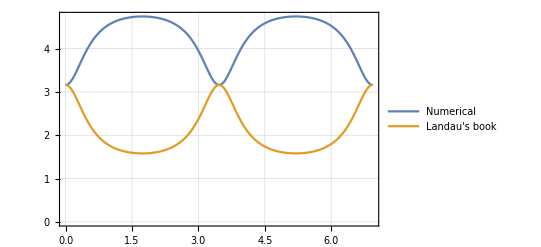

```mathematica
ListPlot[{dϕ1,dϕ2},Joined->True,PlotTheme->"Detailed",PlotLegends->{"Numerical","Landau's book"}]
```

Except for the sign typos, in Zimmermann 1980, the author chose the wrong variable in the theta function.

He dropped the coefficient π  of the second term in the bracket.

### Section 2.2 Numerical approach using quaternions

The rotation matrix R is

Check the rotation matrix:

Check Eqs. (25-28):

```mathematica
q0=Cos[1/2 θ]Cos[1/2(ϕ+ψ)]
q1=Sin[1/2 θ]Cos[1/2(ϕ-ψ)]
q2=Sin[1/2 θ]Sin[1/2(ϕ-ψ)]
q3=Cos[1/2 θ]Sin[1/2(ϕ+ψ)]
```

Cos[θ/2] Cos[(ϕ+ψ)/2]

Cos[(ϕ-ψ)/2] Sin[θ/2]

Sin[θ/2] Sin[(ϕ-ψ)/2]

Cos[θ/2] Sin[(ϕ+ψ)/2]

The rotation matrix represented by Euler angles from the body frame to the inertia frame is

```mathematica
aa={{Cos[ϕ],Sin[ϕ],0},{-Sin[ϕ],Cos[ϕ],0},{0,0,1}};
bb={{1,0,0},{0,Cos[θ],Sin[θ]},{0,-Sin[θ],Cos[θ]}};
cc={{Cos[ψ],Sin[ψ],0},{-Sin[ψ],Cos[ψ],0},{0,0,1}};
EulerRotation=Simplify[Inverse[cc.bb.aa]]//MatrixForm
```

(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ] | -Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ] | Sin[θ] Sin[ϕ]
Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ] | Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | -Cos[ϕ] Sin[θ]
Sin[θ] Sin[ψ] | Cos[ψ] Sin[θ] | Cos[θ])

Here, we check the components R_11, R_12, and R_13:

```mathematica
r11=Simplify[q0^2+q1^2-q2^2-q3^2]
r12=Simplify[2*q1*q2-2*q0*q3]
r13=Simplify[2*q1*q3+2*q0*q2]
```

Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]

-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ]

Sin[θ] Sin[ϕ]

Check the time evolution equation of quaternions (Eq. 29)

```mathematica
<<Quaternions`
qq=Quaternion[qq0,qq1,qq2,qq3];
ωω=Quaternion[0,ω11,ω22,ω33];
jingjing=1/2 qq**ωω;
dqdt=jingjing[[1]]+jingjing[[2]]+jingjing[[3]]+jingjing[[4]];
Coefficient[dqdt,qq0]
Coefficient[dqdt,qq1]
Coefficient[dqdt,qq2]
Coefficient[dqdt,qq3]
```

ω11/2+ω22/2+ω33/2

-ω11/2+ω22/2-ω33/2

-ω11/2-ω22/2+ω33/2

ω11/2-ω22/2-ω33/2

The Euler angles can be recovered by

The comparison of numerical solution and analytical solution is in the jupyter notebook.

### Section 2.3 Physical parameters for triaxial NSs

Constants

```mathematica
G=6.674079999999999*10^-08;
c=29979245800.0;
M14=2.7838655814734013*10^33;
R=10^6;
frot=100;
Ωrot=frot*2*π*1.0;
distance=3.0856775814671917*10^22(*10个kpc的距离*);
modulus=10^30(*the shear modulus of the crust*);
I0=10^45;
```

```mathematica
V=(4π)/3 R^3*1.0
Vc=4*π*R^2*0.1*R;
Eg=3*G*(M14)^2/5/R;
η=57/10*modulus*Vc/Eg
ϵ0=Ωrot^2*R^3/G/M14
η*ϵ0
```

4.18879×10^18

0.0000230805

0.00212481

4.90417×10^-8

```mathematica
0.0000230801728118435
```

0.00212481

4.90417×10^-8

Another estimation of the rigidity

```mathematica
25/2*R*c^2/G/M14*modulus/c^2/(M14/V)*0.1
```

0.000010123

Estimation of the wobble angle: θ_max≈ σ_break/ ϵ_0

```mathematica
0.001/ϵ0
```

0.47063

```mathematica
0.001/ϵ0
```

0.47063

```mathematica
1.5*5.2
```

7.8

```mathematica
0.018*25
```

0.45

### Expansions of the trigonometric functions of three Euler angles

```mathematica
Clear["Global`*"]  (*Clear all variables*)
Normal[Simplify[(I3*b)/J Series[JacobiDN[z,m],{m,0,1}]]]/.m-> 16κ*γ^2
Normal[Series[(1-((I3*b)/J JacobiDN[z,m])^2)^(1/2),{m,0,1}]]/.{J^2-> b^2 I3^2+a^2 I1^2}
```

(b I3)/J-(8 b I3 γ^2 κ Sin[z]^2)/J

√((a^2 I1^2)/J^2)+(b^2 I3^2 √((a^2 I1^2)/J^2) m Sin[z]^2)/(2 a^2 I1^2)

In the expression of cosθ, the second term is a three-order quantity, we can drop it.

```mathematica
cosθ=Normal[Series[Simplify[(b I3)/J]/.(b I3)/J-> 1/(1+γ^2)^(1/2),{γ,0,2}]]
```

1-γ^2/2

For sinθ, it can be expressed as

```mathematica
γ/(1+γ^2)^(1/2)+(16κ*γ^2*γ/(1+γ^2)^(1/2))/(2 γ^2)Sin[z]^2
```

γ/(√(1+γ^2))+(8 γ κ Sin[z]^2)/(√(1+γ^2))

```mathematica
sinθ=Normal[Series[γ/(√(1+γ^2))+(8 γ κ Sin[z]^2)/(√(1+γ^2)),{γ,0,2}]]/.z-> Subscript[Ω, 2]*t
```

γ (1+8 κ Sin[t Ω_2]^2)

Series expansions for cosψ

```mathematica
f1=Simplify[Cos[ArcTan[((1-δ1)JacobiCN[z,m]/JacobiSN[z,m])]]]
```

1/(√(1+((-1+δ1)^2 JacobiCN[z,m]^2)/JacobiSN[z,m]^2))

```mathematica
f2=Normal[Simplify[Series[f1,{δ1,0,2}]/.m->0]]
f3=Normal[Simplify[Series[f1,{m,0,1}]/.δ->0]](*can be dropped, m is third order small quantity *)
```

1/(√(Csc[z]^2))+(δ1 Cos[z]^2)/(√(Csc[z]^2))+(δ1^2 Cos[z]^2 (1+3 Cos[2 z]))/(4 √(Csc[z]^2))

1/(√(1+(-1+δ1)^2 Cot[z]^2))+(m (-1+δ1)^2 Cot[z] Csc[z]^2 (-2 z+Sin[2 z]))/(8 (1+(-1+δ1)^2 Cot[z]^2)^(3/2))

```mathematica
Sin[z]+δ1*Sin[z] Cos[z]^2+1/4 δ1^2 Sin[z] Cos[z]^2 (1+3 Cos[2 z])/.{δ1-> 8κ+32 κ^2}
```

Sin[z]+(8 κ+32 κ^2) Cos[z]^2 Sin[z]+1/4 (8 κ+32 κ^2)^2 Cos[z]^2 (1+3 Cos[2 z]) Sin[z]

```mathematica
Expand[(8 κ+32 κ^2)^2]/.{κ^3-> 0, κ^4-> 0}
```

64 κ^2

```mathematica
cosψ=Sin[z]+(8 κ+32 κ^2) Cos[z]^2 Sin[z]+1/4 64 κ^2 Cos[z]^2 (1+3 Cos[2 z]) Sin[z]/.z-> Subscript[Ω, 2]*t
```

Sin[t Ω_2]+(8 κ+32 κ^2) Cos[t Ω_2]^2 Sin[t Ω_2]+16 κ^2 Cos[t Ω_2]^2 (1+3 Cos[2 t Ω_2]) Sin[t Ω_2]

Series expansion for sinψ

```mathematica
s=Simplify[Sin[ArcTan[((1-δ1)JacobiCN[z,m]/JacobiSN[z,m])]]]
s1=Normal[Simplify[Series[s,{δ1,0,2}]/.m->0]]
s2=Simplify[Series[s,{m,0,1}]/.δ->0](*can be dropped, m is third order small quantity *)
```

-((-1+δ1) JacobiCN[z,m])/(√(1+((-1+δ1)^2 JacobiCN[z,m]^2)/JacobiSN[z,m]^2) JacobiSN[z,m])

Cos[z] √(Csc[z]^2) Sin[z]-δ1 Cos[z] √(Csc[z]^2) Sin[z]^3-3/16 δ1^2 √(Csc[z]^2) Sin[2 z]^3

-((-1+δ1) Cot[z])/(√(1+(-1+δ1)^2 Cot[z]^2))+((-1+δ1) (Cot[z]-z Csc[z]^2) m)/(4 (1+(-1+δ1)^2 Cot[z]^2)^(3/2))+O[m]^2

```mathematica
Cos[z] -δ1 Cos[z] Sin[z]^2-3/16 δ1^2  Sin[2 z]^3/Sin[z]/.Sin[2z]-> 2*Cos[z]Sin[z]
```

Cos[z]-δ1 Cos[z] Sin[z]^2-3/2 δ1^2 Cos[z]^3 Sin[z]^2

```mathematica
Cos[z]-δ1 Cos[z] Sin[z]^2-3/2 δ1^2 Cos[z]^3 Sin[z]^2/.{δ1-> 8κ+32 κ^2}
```

Cos[z]-(8 κ+32 κ^2) Cos[z] Sin[z]^2-3/2 (8 κ+32 κ^2)^2 Cos[z]^3 Sin[z]^2

```mathematica
sinψ=Cos[z]-(8 κ+32 κ^2) Cos[z] Sin[z]^2-3/2 64*κ^2 Cos[z]^3 Sin[z]^2/.z-> Subscript[Ω, 2]*t
```

Cos[t Ω_2]-(8 κ+32 κ^2) Cos[t Ω_2] Sin[t Ω_2]^2-96 κ^2 Cos[t Ω_2]^3 Sin[t Ω_2]^2

Series expansion for ϕ. The periodic part can be expressed as

and the nome q is

```mathematica
q=Series[Exp[-π*EllipticK[1-m]/EllipticK[m]],{m,0,2}]
```

m/16+m^2/32+O[m]^3

So we can drop this term. And we only retain the linear-in-time part

```mathematica
cosϕ=Cos[Subscript[Ω, 2]*t]
sinϕ=Sin[Subscript[Ω, 2]*t]
```

Cos[t Ω_2]

Sin[t Ω_2]

```mathematica
cosϕ
sinϕ
cosθ
sinθ
cosψ
sinψ
```

Cos[t Ω_2]

Sin[t Ω_2]

1-γ^2/2

γ (1+8 κ Sin[t Ω_2]^2)

Sin[t Ω_2]+(8 κ+32 κ^2) Cos[t Ω_2]^2 Sin[t Ω_2]+16 κ^2 Cos[t Ω_2]^2 (1+3 Cos[2 t Ω_2]) Sin[t Ω_2]

Cos[t Ω_2]-(8 κ+32 κ^2) Cos[t Ω_2] Sin[t Ω_2]^2-96 κ^2 Cos[t Ω_2]^3 Sin[t Ω_2]^2